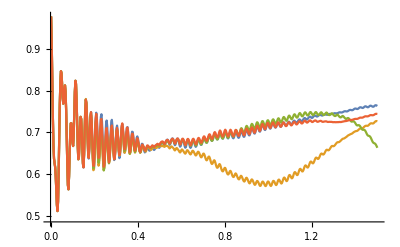

```mathematica
time[x_,y_:1]:={Table[0.002/4*5.308*n/y,{n,1,Length[x]}],x}ᵀ;
ListLinePlot[{
time[{0.9780657988115641,0.9165681615833895,0.8286472857697756,0.7376114394293667,0.6700666393373297,0.6367914502797342,0.6258042492069847,0.616252882488554,0.5940175630702387,0.5594776103560153,0.5254681363547626,0.5107128814620707,0.5337219556345998,0.5988017317618245,0.6857295829828255,0.765796490467145,0.8215903677477732,0.8468016501167801,0.8417187839894738,0.8145942712985462,0.7830457683064795,0.7686258908217999,0.7799598794849394,0.802275866433829,0.8125126814713467,0.7965034520355634,0.751780317902539,0.6873067346393724,0.6207419486935818,0.5730968371161396,0.5629877346268324,0.593767701568513,0.6463503133432571,0.6945649780490174,0.7214446438798177,0.7216410973518325,0.7011494766669253,0.675882107509235,0.6669166607990127,0.6909622858351315,0.7434832782462168,0.7965620874687058,0.823660400529236,0.8163474236374038,0.7792881062724231,0.7242773515985437,0.6690655511845944,0.6352393895140649,0.6388176030828671,0.6741713798272284,0.7148788264303678,0.736952972089296,0.7316751599486302,0.7020280603032644,0.6598212280410597,0.6239935680848685,0.6154764351738268,0.6454230806171957,0.7013664862676784,0.7533749187810332,0.7781778791223374,0.770146118220839,0.7361059246771976,0.6899225481395865,0.6503013875350356,0.6368135038194295,0.6582961034754221,0.700945446994307,0.7373147146526143,0.748281802294589,0.7306828259782668,0.6924268491964496,0.6478377140009111,0.6150306455753166,0.6111931227043391,0.6412543751744526,0.689448870805591,0.7303595246305981,0.7469223723487863,0.7355449567054309,0.7033882629610229,0.6647856828679602,0.6374952069081794,0.636897057894959,0.6651642935968601,0.7058753226943224,0.7364767282413606,0.7433007549511179,0.7246136143687614,0.6885485013553574,0.6495703364807811,0.6241499650669085,0.6250884431442643,0.6522944052846855,0.6900616110063659,0.7191853772271415,0.7281534570657536,0.714554042025385,0.6848726861957071,0.6525606090894078,0.6331635313543037,0.6376860030820173,0.6644417592214847,0.698583503315419,0.7235987434253396,0.7298454413468974,0.7150833399800748,0.6851691108077514,0.6529635556323882,0.6332035498115715,0.6356529909968256,0.6581897374256587,0.6875538070474376,0.7095956654171364,0.7159841420724216,0.7043510293774465,0.6794038719792054,0.652720009454418,0.6378359743241442,0.6431077897974824,0.6656609307284778,0.6932410166935948,0.7136166995000771,0.719903600983266,0.7100739550517944,0.6879852359348672,0.6641353422145859,0.6511738403767732,0.6562083670706857,0.6753738318979178,0.6970459983404999,0.7109626079310273,0.7124711150547748,0.7010934808894402,0.6806036086818409,0.6601516927219808,0.6506247850513183,0.6570973014487257,0.6744256037685799,0.6918013999860632,0.7012893115900768,0.7006491949823159,0.69083966443764,0.6751215799726547,0.6605547085883923,0.6555252865037426,0.6627729814187152,0.6762910525512654,0.6870239859461551,0.6900533315426635,0.6856514549303544,0.6761379887747836,0.6642059124617498,0.6544795016756212,0.6523409922820559,0.6584390047364387,0.6672065464732052,0.67242218548072,0.6718732114859877,0.6671289577408719,0.6609379143896499,0.655128653946595,0.6516316386743536,0.6527512395359023,0.6579321884877318,0.6633088246485322,0.6655335819418469,0.6639072535571532,0.6601846622486186,0.6570758665058141,0.655747362296161,0.6560726016263178,0.6581915583823178,0.6614260598833671,0.663917882628896,0.6642325636392235,0.6620517472367193,0.6588560538777201,0.6573843474630345,0.6587278443014633,0.6615928491626465,0.6646208205280171,0.6671144050429019,0.6685568052052812,0.6684370574683216,0.666344984698142,0.6634704683767693,0.6626405216127234,0.6652373769566976,0.6696008715021712,0.6734124397881908,0.6757555448085443,0.6766868530940903,0.6759862642810702,0.6731642394492644,0.6694138295185484,0.667783933169112,0.6701116323106215,0.6748512383819627,0.6791167450190332,0.6815766980897674,0.6823117516215395,0.6810517387421584,0.6772976600510203,0.6724611163486515,0.6698640294075354,0.6717538801987947,0.6768353264658294,0.6817974630780956,0.6846763642707615,0.6852427409973472,0.6831816822183506,0.6782694831454055,0.672318426183171,0.6688851135151584,0.6704574200063653,0.6758963158039276,0.6814683377861855,0.6845384536186618,0.6846124630466457,0.6815665418262249,0.675662294326526,0.6690901615250685,0.6654101220076025,0.6670815180110149,0.6730441368509466,0.67925420101539,0.6825100866630981,0.6821946520820055,0.6786015772165512,0.672482228387086,0.6661328567547534,0.6628254990462293,0.6647739618342239,0.6710069180377299,0.6775321358363579,0.6809199899502177,0.6805040288096468,0.6768741169015533,0.6710844174495953,0.6653569906975706,0.662512544019985,0.6644078139826942,0.6703221309036159,0.6768041583125595,0.6805458429451189,0.6806721591444914,0.6776750123165419,0.6726319074106528,0.6676202199259932,0.66503708471656,0.666424268468315,0.6714422284002196,0.6775418027945268,0.6818204149111982,0.6830146818204385,0.6811019634156115,0.6769279829664484,0.6723972682272616,0.6696383960709796,0.6700503118733083,0.6737601829990374,0.6792629831641678,0.684184427657889,0.6867165647151103,0.6860573179861157,0.6826975771471414,0.6784437310543927,0.6753073837551391,0.67464269861644,0.6769971580618995,0.6818163281710578,0.6872916162240964,0.6911060369083672,0.691578285371335,0.688797853492707,0.6845574307602197,0.680914917314248,0.6792870851224654,0.6805501914990447,0.6848006715585623,0.6906489209461328,0.6953732115166412,0.6965743350738048,0.6940452829265298,0.6896232047318639,0.6854143551041726,0.6828880556734302,0.6831689996380912,0.6868862715306709,0.6930102655035764,0.6984703455740023,0.7002244442689719,0.6978073138164558,0.693136912404103,0.688419996381392,0.6851696777100271,0.6846536900906093,0.6878478314587796,0.6939836134627635,0.6998083993587597,0.7018882501916369,0.6995856660909189,0.6948400321138086,0.689881288672204,0.6862020871125343,0.6850522471077484,0.6875779872342846,0.693362483377896,0.6993062872532837,0.7017944305487955,0.6999396210008769,0.6955350051692071,0.6907266174575393,0.6869418975015728,0.6853665673329463,0.6872075342091166,0.6924375414621134,0.6984207804030433,0.7015769492568616,0.7006240816328629,0.6969580790470474,0.6924996841513127,0.6886013362597165,0.6864921144969173,0.6875792353144646,0.6922660585095679,0.6984007774902674,0.7024366887509101,0.702623226937445,0.6998299879904295,0.6957409798667831,0.6917064791289103,0.6890602847274087,0.6894001909815068,0.6934962002093097,0.6996854059618761,0.704523502612816,0.7057810430108569,0.7037918257006875,0.700032817510322,0.6958870975224446,0.6928190318161643,0.6925694829448249,0.6961313105966687,0.7022227960254903,0.707638717835738,0.7098416899375465,0.7085986161673864,0.7051084487679257,0.700841098922543,0.6974361434373056,0.6967421370527545,0.6998551691368078,0.7057305490565491,0.711388190681199,0.7141546288023523,0.713402214415694,0.7100910446662193,0.7057347731729997,0.7021645327794092,0.7012948355691992,0.7041180588125612,0.7096369822917435,0.7151444833748251,0.7180462657469739,0.7174931831775841,0.7142551741319889,0.709872279452288,0.7062739502437043,0.7053553790604813,0.7079604390602435,0.7130362754306975,0.7181276583981063,0.7208821318743679,0.7203800146100544,0.717229512659746,0.7129559663304338,0.7094880812543735,0.7085746212487172,0.7108388266232618,0.7152547532144181,0.7197474086406881,0.7223025480343263,0.7219436215503225,0.7190601468848281,0.7150769024397546,0.7118501546930521,0.7109484593199423,0.7128192839074416,0.7165209303735316,0.7203756635917447,0.7227643084204399,0.7226967272300077,0.7202871996947406,0.7167364752566576,0.7137838065665121,0.7128773470128653,0.7143920844213135,0.7175160462771957,0.720929296721963,0.7233399350186028,0.7237686467940314,0.7220250341276547,0.7190070244500003,0.7163006880297617,0.7153239018657536,0.7164961285957877,0.7191361635327298,0.7221725008535171,0.7246159929619409,0.7255373448868137,0.7244581313596344,0.7219440432702133,0.7194484063416514,0.718420765647079,0.7193459333214517,0.7216435362782726,0.7243872234133724,0.7267759644094939,0.7279814448848961,0.7273921286266057,0.7253228160491793,0.723065277962127,0.722026409867117,0.7227714554985922,0.7248209540565803,0.7273188518062789,0.7295672939614385,0.7308698048705339,0.730613694292756,0.7289382912745955,0.7269615809851798,0.7260523827616521,0.7267966288279798,0.7287261804399804,0.7309848902696051,0.7329641893070517,0.734154293648066,0.7340364493411832,0.7326427409829783,0.7309543603027969,0.7302504892685145,0.7310587091863947,0.7328722820178949,0.7348504857036687,0.7364812099102996,0.7374435429514045,0.73735936029453,0.7362128581160503,0.7348150876734666,0.7343039935353953,0.7351329309639919,0.7367549712439088,0.7383325629701978,0.7394435480158171,0.7399903112293356,0.739820665623781,0.7389384227266411,0.737936360219353,0.7376776825694368,0.7384440422844488,0.7397184548517671,0.7408046680519323,0.7414208744890831,0.7416338723713544,0.7414378159105074,0.7408264630262316,0.740171550778378,0.7400937250366503,0.7407892404116411,0.7417923198631903,0.7425038058911437,0.7427395331101412,0.7427016398791078,0.7425430568481912,0.7422478900604274,0.7419628708670344,0.7420535235388214,0.7426475327676215,0.7434057254867021,0.7438902557310322,0.7439710305328936,0.7438549537779559,0.7437689826011349,0.7437460543295774,0.7437997144184897,0.7441067693183971,0.7447172818448885,0.7453711615760695,0.7457153772293882,0.7456613346051175,0.7454512449769013,0.745370610951081,0.7455027901772039,0.7458141563645764,0.746333318507191,0.7470274658749392,0.7476456400869681,0.7479249098286613,0.7478267029497464,0.7475697474849496,0.7474684349281822,0.7476932347107945,0.7482216956250873,0.7489432498408194,0.7497065872294677,0.7502892295078746,0.7505227875905542,0.7504111223718402,0.7501335206993714,0.7499711948064418,0.7501711800810672,0.750791590896986,0.7517011158562256,0.7526587877609656,0.753391854686415,0.7537013486567378,0.7535839199309373,0.7532113138164868,0.752919390062131,0.7530673911886274,0.7537760981002102,0.7548534820133436,0.7559352679581363,0.7566941540293244,0.7569728513285688,0.7567785672570736,0.7562948841089444,0.7558661821637855,0.7559286925696692,0.7566827224647585,0.7578886372320673,0.7590689463425068,0.7598202309061728,0.7599953277836621,0.7596452432412553,0.7589928455909208,0.7584204382782771,0.758386803172706,0.7591344961241013,0.7604121094797551,0.7616177058065947,0.7622600285277199,0.7622138004594206,0.7616194494845169,0.7607671764758972,0.7600883829006667,0.7600536081848346,0.7608317535667976,0.762110836479285,0.7632706751160044,0.7638152159170518,0.7636382497022868,0.7629398485927544,0.7620455422288684,0.7613395635078365,0.7612422525158116,0.7619642186173711,0.7632369312342794,0.7643977055052119,0.7648930290864994,0.7646595189799934,0.7639806893754277,0.7631712951127047}],
time[{0.9780657988115637,0.916568161583386,0.8286472857697638,0.7376114394293387,0.6700666393372848,0.6367914502796749,0.6258042492069172,0.6162528824884783,0.5940175630701608,0.5594776103559432,0.5254681363547035,0.5107128814620251,0.5337219556345639,0.5988017317617929,0.685729582982793,0.765796490467114,0.8215903677477565,0.8468016501167742,0.8417187839894774,0.8145942712985579,0.783045768306484,0.7686258908217914,0.7799598794849001,0.8022758664337517,0.8125126814712357,0.7965034520354294,0.7517803179023876,0.6873067346392199,0.6207419486934304,0.5730968371159935,0.562987734626677,0.5937677015683139,0.6463503133408914,0.6945649779712225,0.7214446423976179,0.721641081021734,0.7011493550537042,0.6758813244523695,0.6669122427175327,0.6909446748471918,0.7434397588852203,0.7964958647709135,0.8235919385186581,0.816282069635319,0.7791958246972864,0.7241022471372074,0.6687452507612327,0.6347482157861327,0.6382485871171573,0.6737361261844662,0.7147390627736284,0.7371224538556301,0.7321384012937967,0.7028657540167372,0.6612382338548168,0.6263652001446042,0.6193082170614154,0.6508139954029502,0.7072594008024823,0.7578836488325864,0.7799456480153361,0.7691553751595022,0.7334700669917462,0.6873357887353692,0.6496802731346557,0.6396506345304882,0.6639805136560389,0.7058184659867816,0.7370379701520235,0.7411890482614851,0.7184298292620763,0.6785388558618436,0.6361860162603253,0.6087756823452015,0.6112644955231316,0.6443481540796592,0.688785770937005,0.7204054515406865,0.7268649441248586,0.7087294164299044,0.6751168439403695,0.6402135572167811,0.6197759754929878,0.6252100712127711,0.6539727009203062,0.688290863865273,0.709535208320738,0.7092745530724367,0.6887332483467196,0.6564990078080738,0.625570333194344,0.6093208068132865,0.6161601008705637,0.6425413205036881,0.6737695477617824,0.6954742703815863,0.7003203272299517,0.6874786702985368,0.6630169988091278,0.6384290130094673,0.6259930153462046,0.6330225402401153,0.6562431459032231,0.6833806805665038,0.7025105819735472,0.707032584586841,0.6954187171888147,0.6724592647841883,0.6486211969289163,0.6354499800392095,0.6398270225863786,0.6591403787700592,0.6828335522166722,0.7002852094185428,0.7053151214941491,0.6960835679815885,0.676291788869762,0.6552938348745673,0.643899231280491,0.6484405745383979,0.666349973995533,0.6879072585425382,0.7034392078902162,0.7076128305180375,0.6990266750776378,0.6808206880362366,0.6613602085834042,0.6505886461547448,0.6539437940768841,0.6684748166014917,0.6852725222272887,0.6961875057786414,0.6974794002009437,0.6887480432557516,0.6727170927388946,0.6563083560246659,0.6478718481556224,0.6514414785066607,0.6636795749484135,0.6768958113690073,0.6848975473267855,0.6856317578120937,0.6794693107963571,0.6682114044003195,0.6566716459717225,0.6511709070433999,0.6544697943888069,0.6634468763819804,0.6722078214945505,0.6765944317307688,0.6759701422115557,0.6713426095649488,0.6636629932229453,0.6555730908427839,0.6513633615264244,0.6530849472559376,0.6587055430062052,0.6643050188945429,0.6669845674045352,0.6665798018565849,0.6643933728025445,0.6607734737207035,0.6563806620914213,0.6536435893201137,0.6544209557212868,0.658063846740418,0.6621386783181086,0.6642208580339641,0.6641228986817442,0.6633987841084912,0.6623101271036745,0.6602070632987909,0.6580971808385639,0.657788315187438,0.6597455906054603,0.6624851542039847,0.6637685027643886,0.6633799762439342,0.663210180880186,0.6638158003786382,0.6637767387151438,0.6627290393156772,0.6620899913389546,0.6630879646604044,0.665040883674231,0.665914574713123,0.6653567028613981,0.6653434544487405,0.6667780680471619,0.6679553654444143,0.6675383473511731,0.6665251309898386,0.6665631915815552,0.6674138012138021,0.6672143857356987,0.6656640528135034,0.6648680621419019,0.6661677277591219,0.667976893851884,0.6682539260232978,0.6672960042597021,0.666648552412643,0.6663404303449346,0.6649475984155037,0.6624794778006957,0.6611547196787697,0.6625408136915711,0.6650951809405875,0.666101413940301,0.6651253194435823,0.6637075371894614,0.662426732121554,0.6603782320050167,0.6576647555359487,0.6563104482917005,0.6578822610802703,0.6609129093361195,0.662297189248235,0.661137574573828,0.6591032966823296,0.6572639851897937,0.6550673469673604,0.6525637334736468,0.6514539649331483,0.6532230031530676,0.6566918184779732,0.6587209045867022,0.6579876978062305,0.6559593054911357,0.6539335812906795,0.6517159510671544,0.6494476561265995,0.648560547296596,0.6504182369390004,0.6541698225901352,0.6568368303474051,0.656688740086608,0.6547842954858537,0.6525101577473043,0.6500616510165539,0.6477347354018796,0.6467287112977246,0.6482351370082455,0.6517915131321194,0.6549283643729331,0.6556655178313425,0.6543259832380666,0.651937867967658,0.648943263498124,0.6459750790150072,0.6442540547709596,0.6449389839589067,0.647995061532606,0.6515258273596362,0.6533278263011391,0.6527775298637831,0.6503090741360918,0.6465729707456428,0.6426877198857309,0.640088839001188,0.6399216814394273,0.6423701864554595,0.6459997873615176,0.648550178280286,0.6486490668854449,0.6461527925047539,0.6418048340230392,0.6370947946757876,0.6336359988634922,0.6325659402463005,0.6342369462994526,0.6377077361980416,0.6408578208865736,0.6417135890673454,0.6395049240699426,0.6349258463212718,0.6297139433895077,0.6256271105519151,0.6238002941529552,0.6247178198149611,0.6278493554364836,0.6313374879634491,0.6328764891207423,0.631162681773731,0.6267059021653468,0.6213576343034755,0.6169897445464582,0.6147349148356707,0.6150989274016996,0.6178501372471341,0.6214935230808141,0.6236372355341939,0.6225827662280045,0.6185878812596083,0.6134681130009288,0.6090813160753391,0.6064732876786064,0.6061492764707114,0.6082170485446,0.6117259798656531,0.6144339726565873,0.6142716009440788,0.6110988293086773,0.6065456355748492,0.6023704463353027,0.5995326911811178,0.5985500170479331,0.5998838757767507,0.603199032499114,0.6065197267512239,0.6074159386286871,0.6052010412681597,0.6012147877167091,0.5971741722439692,0.5940773182193658,0.5924906326857856,0.5930762923797747,0.5959665697536246,0.5995593703265703,0.6012607423962764,0.5999142066191548,0.5965292554585931,0.5927052861726877,0.5894029645422357,0.5871949035847646,0.5869356888439289,0.5892394811612719,0.5929455976789766,0.595404930488203,0.595007952531085,0.5923375295163027,0.5888078521925025,0.5853619177930232,0.5826273371673815,0.5816069824042552,0.5832919198402908,0.5870018713680443,0.5901755265032019,0.5907437167225038,0.5887872757455905,0.5855308191042273,0.581974442557272,0.5788426758381754,0.5772290447908969,0.5783432798660165,0.5818887001599701,0.5855055827878074,0.5868655882671012,0.5856167101643441,0.5827592040762972,0.579274775190435,0.5759171351550938,0.573776079395118,0.5741706955116352,0.5771977817118422,0.5809317470421498,0.5830177507135461,0.5826493373383177,0.5804543112018763,0.5772944655359509,0.5739212580482133,0.5714291770883779,0.5712500220254667,0.5739023472948249,0.5779277691994091,0.5809339921790714,0.5816202940860301,0.5802137272211284,0.5774503517929456,0.5741129930089784,0.571349202195769,0.5706892158465996,0.5729131288660203,0.5769429219965869,0.5804777354259817,0.5818792027738959,0.5810056053347781,0.5784938485057713,0.5751616290727634,0.5721495939827789,0.5709944761298723,0.5727306917651405,0.5767294076424554,0.580857331459198,0.5831513702050938,0.5830279090133309,0.5809418765971224,0.5777183861340902,0.5745626861334475,0.5730879629074097,0.5744838346773374,0.5783987648693951,0.5829016966518692,0.5858630791640386,0.5863363407025104,0.5846263032905153,0.5816053630075761,0.5784877541190018,0.5768098482192765,0.5778325953328396,0.5815291965222339,0.5863162945268439,0.5900199001912957,0.5913330588295451,0.5902589921755586,0.5875768917124541,0.5844960134038729,0.5826106979757616,0.5832906535804291,0.586695908476274,0.5914845572380324,0.5955630800815157,0.5974055408658226,0.5967792759276286,0.5943875680787932,0.5914189162338341,0.589432855685803,0.5897976444668489,0.5927961448102138,0.5973935574932987,0.6017164118712084,0.6041053924511892,0.6040313884645014,0.6020184849490796,0.5992090991470737,0.5971900379004189,0.5973840400109977,0.6001232011855038,0.6045368664938716,0.6089551761181647,0.6117093287683681,0.6120683540638949,0.610417156563429,0.6078569384891294,0.6059540392049684,0.6060761753675357,0.6085236990149365,0.6125563424044715,0.6167923725295911,0.6197051563280856,0.6204578642897156,0.619248923257139,0.6170496460402716,0.6153489792106923,0.6154681298643677,0.6176770170531926,0.6213680342288483,0.6254465705370877,0.6285542033873752,0.6297386726947626,0.6289780061155357,0.6270934771515387,0.6254918431155939,0.6254897693488954,0.6273914179324405,0.630679957006949,0.6344762351037508,0.6376250605912422,0.6391232167178212,0.6387590926033996,0.6372383418137202,0.6359262409764426,0.6360657585352366,0.63786295562165,0.6408030668911587,0.6442061845569004,0.6471755305000099,0.6487986093964724,0.6487407680534215,0.6475529598624962,0.6464847345300402,0.6466596236274429,0.64820525338706,0.6506366034591275,0.653470891420084,0.6561039980145824,0.6577758826086009,0.6580509871742584,0.6572881682690995,0.6565608160233067,0.6568454907536332,0.6582147044784011,0.6602359365688971,0.6625737527419074,0.6648689023483155,0.6665523692978951,0.6671585750709724,0.6668557771246175,0.6664912380058154,0.6668770974874998,0.6680727064638264,0.6696998674091376,0.6715302805372031,0.6734362416077585,0.675069831645066,0.6759863989208503,0.6761455409766571,0.6761250900371513,0.6765949958207746,0.6776290607222983,0.6788920676875582,0.6802185303958196,0.6816549979617957,0.6830899957465199,0.6841610752204565,0.6846708733027576,0.6849573423064997,0.685530894184673,0.6864509148319026,0.6874286710843629,0.688356199521476,0.689407048189114,0.6906772552199717,0.6919169681402768,0.6928192934017364,0.693469243463129,0.6941848250644795,0.6949910959384693,0.6956452859263432,0.6961095947645128,0.696688447703842,0.6976555158941325,0.6988787204857319,0.6999988846896169,0.7008800668436366,0.701653540400647,0.7023358866849037,0.7027611831851465,0.7029489870360309,0.7032643815743271,0.7040936027407074,0.7054048250213871,0.706782034794799,0.7078824148933784,0.7087010473794072,0.7092682166742676,0.7095075617019827,0.7094828233996524,0.7095745513858366,0.7102013894073463,0.7114089931580231,0.7128187526344985,0.7140352593372936,0.7149464872255792,0.7155237998088936,0.715690630132897,0.7155344298128894,0.7154558460313512,0.7159410419805663,0.7171135270901147,0.7186253220975528,0.7200082590032624,0.7210001268066657,0.7215035299641992,0.721511017845604,0.7211990873476183,0.7209716781788826,0.7212914746008734,0.7223418262284961,0.7238386937780124,0.7252805977653966,0.7263310337519281,0.7268408498826211,0.7267896925124634,0.7263741445408932}],
time[{0.9780657988115637,0.916568161583386,0.8286472857697635,0.7376114394293374,0.670066639337283,0.6367914502796713,0.6258042492069181,0.6162528824884821,0.5940175630701667,0.5594776103559481,0.5254681363547046,0.5107128814620243,0.5337219556345645,0.5988017317617924,0.685729582982793,0.7657964904671194,0.8215903677477671,0.8468016501167814,0.8417187839894815,0.814594271298565,0.7830457683064873,0.7686258908217892,0.7799598794848942,0.8022758664337443,0.8125126814712342,0.7965034520354322,0.751780317902393,0.6873067346392246,0.6207419486934364,0.5730968371159965,0.5629877346266817,0.5937677015683459,0.6463503133430859,0.6945649780488519,0.7214446438796793,0.7216410973517293,0.701149476666856,0.6758821075091951,0.6669166607989945,0.6909622858351118,0.7434832782461709,0.7965620874684903,0.8236604005252445,0.8163474235779214,0.7792881057582655,0.7242773490891187,0.6690655481413104,0.635239469557651,0.6388183777242048,0.674174576977715,0.7148861374298717,0.7369664005560526,0.7317081189155495,0.7021245282973068,0.6600766932231125,0.6245793816827151,0.616611889354192,0.6471477513423632,0.7032360698078479,0.754652921786935,0.7784869986227818,0.7698046012753029,0.7359806678212176,0.6911847705264654,0.6542361989695518,0.6442208233651612,0.6681249200162633,0.7097700271671262,0.7414838279125539,0.746513330119513,0.7243689257647794,0.6844901482749667,0.6416262426803492,0.6134500617504542,0.6152098968936169,0.6478938679882258,0.6924911322516816,0.7248796722188188,0.7325286561287636,0.715559866826316,0.6826012634673194,0.6476942581649737,0.6268528176617228,0.6318732226969968,0.6603913671351348,0.6944444422898111,0.7151195609878219,0.7139296457841217,0.6921589474010701,0.6584599371749423,0.6259622023941219,0.6082551942163451,0.6139886060539741,0.6397511851726485,0.6708061833278636,0.6926948077668161,0.6980354154954692,0.6858600441861525,0.6619791571448507,0.6377145275983335,0.6253907922398732,0.6325227491002577,0.6560398091829464,0.6837253422405929,0.7035147400683363,0.7085953868035957,0.6972664891291824,0.6741941362937272,0.6497968510276463,0.6357660325021934,0.6393867935816672,0.65851431135305,0.6827019458566318,0.7009965577458547,0.7068165781747194,0.6981101699281054,0.6784916620160723,0.6573138668771845,0.6456265432823476,0.6502676179651462,0.6690865638228952,0.6921964352398139,0.7092896047203402,0.7144913370669939,0.7061887270013273,0.6874984501357391,0.6669584505644451,0.6550099289450022,0.6577698001973445,0.6726026987256843,0.6901506688720718,0.7014988854347682,0.7025053582182592,0.6928355845888584,0.675471843550151,0.6576873959767715,0.6483260439182715,0.6518760832195297,0.6649466077292984,0.6792224095725828,0.6878686192294977,0.6885973543408894,0.6819068455237774,0.6699014600628604,0.6577482290973683,0.6521426878965844,0.6559721092333333,0.6657164709004495,0.6748708448283567,0.6790032258088249,0.6775817181175737,0.671906722389787,0.6633018484643356,0.6547484763832109,0.650727990809804,0.65311099712439,0.6593036043934618,0.6649720402994704,0.6672889570070267,0.6664206547767872,0.664010700882618,0.6606755494195553,0.6571469625916294,0.6556270612220653,0.657425785298957,0.6613642198389112,0.6649819741397497,0.6663082295462319,0.6656813701246072,0.6649895097999777,0.6645675249898438,0.6635683631742493,0.6625221686450329,0.6626650613325483,0.664175864127581,0.6658293543051699,0.6659852072736551,0.6649529097977277,0.6648801847031979,0.6663173290312181,0.6675557746136881,0.6676787978535399,0.6675584021192023,0.6682181953134844,0.669240301847488,0.6691215426464433,0.668023100157953,0.6681964836807778,0.6705795965353955,0.6732234270404102,0.6742439930424929,0.6740693150587775,0.6741103010066906,0.6743374687312351,0.6733616355752343,0.6713714539810336,0.6707682647672328,0.6729352117545239,0.6760931554961184,0.6777891533303683,0.6779216431772247,0.6778751869750633,0.677700918338668,0.6760932693536178,0.6733773147823054,0.6721562141902551,0.6742308315968863,0.6780751301429121,0.6807519365054917,0.6814920435355267,0.6814423547158017,0.6807192492132116,0.6782529754165815,0.674626055472928,0.6726133654209386,0.6743189287652125,0.6784918748699319,0.6818792441907258,0.6830369920437014,0.6827368518095467,0.6812079511942265,0.677808087730089,0.6734169180363123,0.6708278754154474,0.6722567722499522,0.6767501561355476,0.6808838435190424,0.6825485222947871,0.6821221725682098,0.6800499641587399,0.6761678968551993,0.6715334937883499,0.6687428191894543,0.6699513556300429,0.6745294305400565,0.6791735125989191,0.6813193296473391,0.6809227188404429,0.6785726536433809,0.6745377478103827,0.6699977694640582,0.6672491114906303,0.6682230014427795,0.6726024435588682,0.6775267177281241,0.6802995948991952,0.6804608787724257,0.6785089968945556,0.6748898038451776,0.6707690347596328,0.6681354026683715,0.6686775730194334,0.6724358481606343,0.6773030934629704,0.6807753259451723,0.6819018654817726,0.680751546165081,0.6776907427050846,0.673860866110035,0.6710857753694034,0.6709455337624586,0.6738801554605983,0.6786051628802554,0.6829278952489899,0.685296550695517,0.6850888152248279,0.6824996210055003,0.6787700771147511,0.6757131322057058,0.674860603066791,0.6769584937803272,0.6814522726206158,0.6865180966466535,0.6900667324215283,0.6906972511752025,0.6883658857271681,0.6844603604313777,0.6809070378188483,0.6792830256075948,0.6805283438147393,0.6846145544862118,0.6900553565103333,0.6943468823544178,0.6954523722810411,0.6931605314583651,0.6890037545752974,0.684995502306029,0.682689448230937,0.6831149236027766,0.6866229666049097,0.692080038044228,0.6968277779520134,0.6983918357799808,0.6963511460107146,0.692249556237216,0.6880770835301684,0.685281628007177,0.6849187185800549,0.6876866388049242,0.6929313333527011,0.6980586237811686,0.7002349099770555,0.6987037238050096,0.6949024432291834,0.6907568880414673,0.6876285348556974,0.6865646810102636,0.6885619157740781,0.6934845647952975,0.6989887319895741,0.7019754921235581,0.7012528724893361,0.6979954897834149,0.6940365730418754,0.6906989216584228,0.6890812519401404,0.690413959652755,0.6949922346491053,0.7008143500075682,0.704651809439464,0.7049015209259294,0.702398734748006,0.6987768235491374,0.6952895100580275,0.6931190152200207,0.6937302584037023,0.6978640221485879,0.7039396710420412,0.7086758264808942,0.7099434465726306,0.7080836549987995,0.7045988555054445,0.7008723990971504,0.6982511754051645,0.698327604482717,0.7020332744338603,0.7081114851118051,0.7133852054991039,0.7153918422284175,0.7140551510072358,0.710736974885819,0.7068529063863851,0.7038253193091837,0.7033294290307336,0.7064454325248822,0.7122175355340186,0.7176989421844542,0.7202216477903849,0.7193091023514305,0.7161015305271957,0.7120518531031805,0.7087075338155606,0.7077640140177147,0.7102960230879107,0.7155819271063026,0.7210247608573306,0.7239366230996073,0.7234630234606068,0.7204836844160636,0.7164466427407814,0.7129272608944633,0.7115941003154379,0.7135282051161129,0.7182284544786788,0.7234629093136757,0.7266354989455429,0.7265840588221429,0.7238717524713422,0.7198739840449815,0.7162210148312715,0.7145735930806794,0.7159704849924522,0.720068757604271,0.7250174180568558,0.7284098786589392,0.7288529476685749,0.7265730303369625,0.722797637963855,0.7191317004404606,0.7172357480834973,0.7181870095705509,0.7218130908218501,0.7265516343961499,0.7301703836817736,0.7311212909005227,0.7293478813302133,0.7259136095027613,0.7223623552696441,0.7202966241095411,0.7208047985240713,0.723883368608056,0.7283080579806324,0.7321137222205719,0.733660530574216,0.7325139921217083,0.7294492244896874,0.7259380147742305,0.7236367423633657,0.7237335850528156,0.7263605431518575,0.730502339153048,0.7344585982015678,0.7365880858347172,0.7361424056350911,0.7335927063188294,0.7302900056827335,0.727856132291519,0.7274971943814689,0.7294837211701524,0.7331118087065622,0.7370146323731951,0.7396120501369647,0.7398501834905269,0.73783355739904,0.7347374167014195,0.7321621295383309,0.731375596226068,0.7327942939651224,0.7359328211740738,0.7396685491317359,0.7424989333636767,0.7431957542536427,0.741581650504889,0.7386528348879122,0.7360189263078878,0.7350190052173009,0.7360600752335749,0.7387147237841449,0.7421204978105663,0.7450287220399582,0.7461451978926265,0.7449608497567634,0.7422236754142134,0.7395117111712984,0.7382049505315158,0.7387254486873306,0.7407271065288672,0.7435977567343452,0.7464098998173905,0.7478976447643182,0.7472424007440158,0.744826786305874,0.7420776805153527,0.7404441310662787,0.7404611827373803,0.7418670803309798,0.7442149297645418,0.7468276474231345,0.7485425914583413,0.7483309844397074,0.7462466493331595,0.7435299116383316,0.7416639664427387,0.7412683540933945,0.7421505667017543,0.7439935421307546,0.7463389878225376,0.7481815957720391,0.7484099602994645,0.7467613217580967,0.7442047688759219,0.7421760557939591,0.7413997580281994,0.7417897421712903,0.7431674136745927,0.7452944142772873,0.7473272385361106,0.7480081535029459,0.7467604093097018,0.7443937026188807,0.7423725422303064,0.7414736085165259,0.7416012137576634,0.7426207114337938,0.7444339272997059,0.7464002933421746,0.7473591737686502,0.7465815640636231,0.7445924497512479,0.7426973522503688,0.7416113989589672,0.7412357238772476,0.7415352215514275,0.7426770645033334,0.7443735447013733,0.7455934636411966,0.7453502608021886,0.7437627347430101,0.7418510524021504,0.7403397333365102,0.7393142553523275,0.7388935981978146,0.7394165459662221,0.7408061203541229,0.7421833204034382,0.7424315589139912,0.741287368714558,0.7395220217810416,0.7378758028335954,0.7365239828729846,0.735666026922318,0.7357545218944118,0.7369191760714452,0.7384401854770529,0.739133617986872,0.7384654236995375,0.7369820555550456,0.7353655005666668,0.7338129467550188,0.7325234283973437,0.7319689129321884,0.7324485333340407,0.7335361533658766,0.7342209270442756,0.7338234901981842,0.732567922750464,0.7309201048475341,0.7290237060204335,0.7271110485549147,0.7257517311568076,0.7254119595256939,0.7259430923973623,0.7265100274149272,0.7263320389525902,0.7253308231836133,0.7237317948165953,0.7216522216075619,0.7193310865165683,0.7173802232473532,0.7164110111271003,0.716495169320302,0.7169910518013256,0.7170592769933747,0.7163579675853881,0.7149093994071487,0.7127805706862496,0.7102362520682209,0.7078661631546379,0.7063275415666331,0.7058742149312254,0.7060540528155824,0.7060468587820189,0.7053110799513943,0.7037100309707999,0.7012790218356979,0.6982872277373052,0.6953166796606305,0.6930451595809461,0.6918323771818481,0.6914039758906707,0.6910326335910087,0.6901154863303457,0.6883883592480382,0.6858286152820258,0.6826721126059713,0.6794222895572786,0.6766972937609955,0.6749241960807706,0.6740294656980007,0.6734694123762166,0.6726223235365832,0.6710858481180556,0.6687354966286464,0.6657814662556704,0.6626854545581288}],
time[{0.9780657988115641,0.9165681615833897,0.8286472857697764,0.7376114394293675,0.6700666393373288,0.6367914502797326,0.6258042492069831,0.6162528824885511,0.5940175630702308,0.5594776103560078,0.5254681363547563,0.5107128814620716,0.5337219556346041,0.5988017317618302,0.6857295829828333,0.7657964904671519,0.8215903677477875,0.8468016501167995,0.8417187839894821,0.8145942712985559,0.7830457683064862,0.7686258908218104,0.779959879484949,0.8022758664338316,0.8125126814713459,0.7965034520355543,0.7517803179025309,0.6873067346393643,0.6207419486935752,0.5730968371161387,0.5629877346268396,0.5937677015685215,0.6463503133432712,0.6945649780490358,0.7214446438798394,0.7216410973518599,0.7011494766669496,0.6758821075092531,0.6669166607990279,0.6909622858351386,0.7434832782462234,0.7965620874687114,0.8236604005292373,0.8163474236374085,0.7792881062724257,0.7242773515985471,0.6690655511845999,0.6352393895140724,0.6388176030828765,0.67417137982725,0.7148788264308873,0.7369529721029998,0.7316751601788345,0.7020280628840585,0.6598212493157385,0.6239937165230897,0.6154773118626308,0.6454267845150747,0.701376230870942,0.7533908999487503,0.7782000037871094,0.7701938356619621,0.736242152472367,0.6902736246815215,0.6510696533713664,0.6382023936322052,0.6602208501696412,0.7027958715589023,0.738356293837849,0.7483512017731877,0.7303446265481108,0.692691053474507,0.6498790338937181,0.6198957751821912,0.6190638254438413,0.6503671922739822,0.6964089384118657,0.7325570158166995,0.7442689651217567,0.7299693407093341,0.6975899586103941,0.6613300476991977,0.6380683061688663,0.6411725285549473,0.6699573033740788,0.706698534059034,0.7308195328430477,0.7318973648652635,0.7102367354189371,0.6744544367377175,0.638395916337416,0.61700761169182,0.620679964924248,0.6470556280335706,0.6805304387303721,0.7045886275224468,0.7104633890303734,0.6969249255114581,0.6702295645066213,0.6426200245295364,0.6276851808154523,0.6341374186942016,0.6591105514233239,0.6891758056359926,0.710734726199432,0.7161576911987079,0.7036200426606297,0.6781843180962364,0.6511140949740372,0.6351486643618245,0.6383840939370761,0.6586226815492132,0.6845136407053426,0.7041730848037395,0.7104714066791925,0.7011508569595344,0.6801184958869673,0.6574590824186161,0.645088646539467,0.6504121191085845,0.6710708258628985,0.6963446969211012,0.7151917687173479,0.7212965699634423,0.7127917924755833,0.6929795684723099,0.671121727538351,0.6586151691156624,0.6621693671825586,0.6788047826313117,0.6981332187646923,0.7104341092836083,0.7112769871875705,0.7003588563017515,0.6810870624411752,0.6615921939743215,0.6516974820763614,0.656317627504729,0.6713711190799778,0.6872511823698167,0.6963801939232184,0.6964466042256452,0.6882347143262536,0.6744013607711463,0.6609671238719173,0.6554359976690681,0.6607262457490944,0.672219109989242,0.6821319692605216,0.6857106355483871,0.6827988823152096,0.6751758190615377,0.664790807131767,0.6554117375174072,0.6520026516566572,0.6559878144883069,0.6634763168259298,0.6692159611591268,0.6705543587213049,0.6682240022832796,0.6643181144396927,0.6599661549896677,0.6564611357139125,0.6561447144341944,0.6596322229672136,0.664619116529872,0.6681233399917048,0.6685205224980977,0.6666817458560432,0.6648896160810864,0.6638891892905355,0.6632167475904946,0.6633854704318546,0.6649657289031433,0.6672479422743386,0.668669880987096,0.6679104959753057,0.6657721977809206,0.6647920402731909,0.6658776934344848,0.6675884451457023,0.6689108577173961,0.6701003157351407,0.6714517428218764,0.6722808662641733,0.6713613834697537,0.6693004340670106,0.6687202250488246,0.6708799989176671,0.6740527402854618,0.6762316560863796,0.6772638849398263,0.6778903637600503,0.677842418991471,0.6760056205660391,0.6730188824005003,0.6716459588574122,0.6735511614425214,0.6771618071825266,0.6799170587893347,0.6811784407927255,0.6816695631365884,0.6811670621194824,0.6786344543964101,0.6748750779302182,0.6728403588140045,0.6745737622042205,0.6787416131425976,0.6823433970017178,0.6841074052788221,0.6845224455290363,0.6834113880402157,0.6799770174482266,0.6753036984331798,0.6725361667734365,0.673998667553509,0.6785543724084935,0.6828080636915271,0.6848660549280933,0.6849644594884748,0.6830777391712873,0.678802291699683,0.6735158179049577,0.6703886585303678,0.6718264221329701,0.6768895824041029,0.6819417929307159,0.6844572905831577,0.684371275937538,0.6819443558551954,0.6772691841625698,0.6719039685914512,0.6688154862326188,0.6702734190171286,0.6755465224027071,0.6810657867038865,0.6839361333095235,0.6838293967103999,0.6812178682725736,0.6765789268574132,0.6715168409283824,0.6686277853339242,0.6698905764689607,0.6748669913114846,0.6805000566586642,0.6838698308031824,0.6842954095006154,0.6821714402799223,0.6781140716454357,0.673626205908829,0.6709314065146784,0.6717399182960626,0.6759485951957992,0.6812901054328566,0.68516487718565,0.6865143689894122,0.6852931213819792,0.6819477160488518,0.6778589685698071,0.6750079700262236,0.6749574891258933,0.6780111521469119,0.6828479664335981,0.68735741469719,0.6899661327031825,0.6898902684060761,0.6872760359297636,0.6834382929752284,0.6802518545475889,0.6792670989086534,0.6811910806469482,0.6855112081249719,0.6905696940097282,0.6943213814778345,0.695231138109155,0.6931402492301149,0.689376436206459,0.6857909697997541,0.6839440848667301,0.6848625327495044,0.6886900889197424,0.6941593402577892,0.6988219897892387,0.7004452029014717,0.6985815265965329,0.6946203915692841,0.6904926641868994,0.6878052566510663,0.6877945225655925,0.6911011372544602,0.6968221690163966,0.7021801509846837,0.7043034181681612,0.702497669689863,0.6982631188517991,0.6936280418823638,0.6902510205826204,0.6894988248236945,0.6923020882287625,0.6980104967480417,0.7037040579407685,0.7061200282269313,0.7043813414751167,0.7000323560849935,0.6951329992991401,0.6912704072780055,0.689845526754633,0.6920201623293184,0.6974318043800279,0.7032443999575035,0.7060303687283112,0.7047113156364848,0.7007139954415529,0.6959863517541435,0.6919974480116908,0.6900751739930713,0.6915178588647108,0.6963947026307109,0.7022945159108425,0.7057561919241315,0.705315242713701,0.7020106101262871,0.6975974909934904,0.6935053482025348,0.6910910218004829,0.69177762361309,0.6960330478809402,0.7019640180313396,0.7062084232360786,0.7068061254837095,0.7042647792743101,0.7001342106151828,0.6958668422961449,0.6929281603461084,0.692924842058033,0.6966034545923204,0.7024725842171372,0.7073278852891106,0.7088685909281779,0.707124359697552,0.7033877514122974,0.6990783321792244,0.6957745837072382,0.6952284329354879,0.6984096624568027,0.7041811912924453,0.7095238368101399,0.7118656526643521,0.7107690806532809,0.7073246297662212,0.7030092902617743,0.6995078402780874,0.6986614484058654,0.7015398975509517,0.7071991247629278,0.712836622826496,0.7157696161043767,0.7152001921748742,0.7120038761902284,0.7077183831152787,0.7041664656611116,0.7031947028145745,0.7057790346985472,0.7110732923913284,0.7165550018413065,0.7196441419481026,0.719308578482028,0.7162241827717223,0.7119410397959283,0.7083559368079195,0.7072597259510265,0.7095051861796878,0.7142754067183971,0.7193563044218312,0.722366393866191,0.7221250641802343,0.7191073378642713,0.7148401951363241,0.7112496637700555,0.7100595070726985,0.7119548556992275,0.7161160995944569,0.7206305462624301,0.7234176567518933,0.7232920775989911,0.7205434099235317,0.7165723131187663,0.7131848863017943,0.7119372415057365,0.713416579391712,0.7169010422672514,0.7208172880383,0.7234645383924055,0.7236828738166987,0.7214313936260159,0.7178129192800647,0.714535144099125,0.7131439545775088,0.7141922209445442,0.7170395445434649,0.7204220398666195,0.7230086772786093,0.7236899408933625,0.7221247121466173,0.7190844422602444,0.7160956058562332,0.7146335258877828,0.7152772572679491,0.7175486528512396,0.7204788304668276,0.7230411661010118,0.7241845236426321,0.7232944330336438,0.7207941331556733,0.7180350478809812,0.7164828504458752,0.7168254869931856,0.7187102624170493,0.7212964524060704,0.7237438149692939,0.7251586847174187,0.7248035421914643,0.7228049640536682,0.7203318588207797,0.7188280960760306,0.7190057322617461,0.7205494944147326,0.7227171555007508,0.7248893815955504,0.7263725961368707,0.726384120561998,0.724795294793834,0.7225741758753289,0.7211170305833309,0.7211736859119348,0.7224752122924429,0.724315628922795,0.7261784177454017,0.7275541394942074,0.7277354095930708,0.7264633995659361,0.7245297066471222,0.7232271438653165,0.7232598950853458,0.724345342289617,0.7258210177292747,0.7272680761605996,0.7283695131463237,0.728570617844504,0.727552606610262,0.7258894642452696,0.72469321420207,0.7246323213189153,0.7254613225761364,0.7265279440940635,0.7274787269863018,0.7282029139723376,0.7283674383259132,0.7276290056604973,0.7263092283961101,0.7252732180844897,0.7250838829189131,0.7255546627248639,0.7261662089912758,0.7267015575280082,0.7271872108428382,0.7273932829578208,0.7269422968633014,0.7259573943294544,0.7251327897589369,0.7249789207518709,0.7253256445587112,0.7256975797426157,0.7259156585902142,0.7261072130697904,0.7262296093382349,0.7259939170299905,0.7253758018081166,0.7248324336135675,0.7247396833887769,0.7249442549581724,0.7250580621597902,0.7249843262174815,0.7249210652021475,0.7249579654838864,0.7248794627560481,0.7245511172247076,0.7242223988056913,0.7241800673818152,0.7243230079451272,0.7243501053825667,0.724192787170133,0.7240803410421723,0.7241605694478849,0.7242928568507168,0.7242943637322742,0.7242626743488995,0.7243801798984935,0.7245769955803156,0.7246391151294003,0.7245494986197238,0.7245377879688281,0.7247768824085637,0.725169843211049,0.7255094490241566,0.7257776710910798,0.7260927257123934,0.726433643700305,0.7266727273037704,0.7267987918576065,0.7269551392945277,0.72726692962839,0.7276973877748709,0.7281253585286521,0.7285142094629135,0.7289120667108667,0.7292724160007915,0.7294727439651312,0.7295108052646844,0.7295455673792126,0.7297262931555845,0.7300691009591942,0.7305049024270076,0.7309896366797347,0.7315049499567465,0.7319280949582182,0.7321134879083879,0.732073110679752,0.7320052985325154,0.7321034365141477,0.7324605388331384,0.7330418342115401,0.7337490336815685,0.7344700667610432,0.7350005906781714,0.7351913890440809,0.7351116975891023,0.7350094828575557,0.735120184209731,0.7355435522647553,0.7362202309969397,0.73700723156309,0.7377408175622316,0.7382303611322014,0.738366981791611,0.7382459609195112,0.7381045039896695,0.7381338795963786,0.7384302876149826,0.7390021271561021,0.7397808899708841,0.740570987054612,0.7410945732774489,0.7412162029242049,0.7410491921603739,0.7408370538430271,0.7407950941502919,0.74103873699475,0.7416199915336592,0.7424919633682806,0.7434233864612971,0.7440761638324512,0.7442834769289304,0.7441557679652014,0.7439648742288714}]
}[[{1,2,3,4}]],PlotRange->{{0,1.5},All}]
```